## 1 step: R -> B -> P1

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5]
e1 =ksyn -k1*L1*r+kd1*b1+kd1*p1-ki*r==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1-ki*b1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kis*p1==0;(*P1*)
(**)
e4 =ksyn -k2*L2*r+kd2*b2+kd2*p2-ki*r==0;(*R*)
e5 = k2*L2*r-kd2*b2-kp*b2+kdp*p2-ki*b2==0;(*B1*)
e6 = kp*b2-kdp*p2-kd2*p2-kis*p2==0;
```

### Solutions

```mathematica
solx=Solve[{e1,e2,e3},{r,b1,p1}][[1]];
r1 = ((p1)/.solx);
solx=Solve[{e4,e5,e6},{r,b2,p2}][[1]];
r2 = ((p2)/.solx);
(*Discrimination ratio defined for infinite ligand concentration*)
ex1[δ_,β_,γ_,ω_,ρ_]=FullSimplify[Limit[(r1/r2)/.{u1->u,u2->u},u->Infinity]];
```

## 2 step: R -> B -> P1 -> P2

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8]
e1 =ksyn -k1*L1*r+kd1*b1+kd1*p1+kd1*q1-ki*r==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1-ki*b1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1-ki*p1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kis*q1==0;
(**)
e5 =ksyn -k2*L2*r+kd2*b2+kd2*p2+kd2*q2-ki*r==0;(*R*)
e6 = k2*L2*r-kd2*b2-kp*b2+kdp*p2-ki*b2==0;(*B1*)
e7 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2-ki*p2==0;(*P1*)
e8 = kp*p2-kdp*q2-kd2*q2-kis*q2==0;
```

### Solutions

```mathematica
Clear[ex2]
solx1=Solve[{e1,e2,e3,e4},{r,b1,p1,q1}][[1]];
r1 = ((p1+q1)/.solx1);
solx2=Solve[{e5,e6,e7,e8},{r,b2,p2,q2}][[1]];
r2 = ((p2+q2)/.solx2);
ex2[δ_,β_,γ_,ω_,ρ_]=FullSimplify[Limit[(r1/r2)/.{u1->u,u2->u},u->Infinity]];
```

((1+β γ+ω+ρ ω) ((γ+δ) (β γ+δ)+(γ ρ+2 δ (1+ρ)+β γ (2+ρ)) ω+(β+ρ+ρ^2) ω^2))/((β γ+δ+ω+ρ ω) ((1+γ) (1+β γ)+(2+(2+γ) ρ+β γ (2+ρ)) ω+(β+ρ+ρ^2) ω^2))

((1+β γ)^2+(2+γ+β γ) ω-(-2+β) ω^2)/((1+β γ+ω) (1+β γ^2+ω (2+β ω)+γ (1+β+2 β ω)))

## 3 step: R -> B -> P1 -> P2 -> P3

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10]
e1 =ksyn -k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1-ki*r==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1-ki*b1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1-ki*p1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1-ki*q1==0;
e5 = kp*q1-kdp*f1-kd1*f1-kis*f1==0;
(**)
e6 =ksyn -k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2-ki*r==0;(*R*)
e7 = k2*L2*r-kd2*b2-kp*b2+kdp*p2-ki*b2==0;(*B1*)
e8 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2-ki*p2==0;(*P1*)
e9 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2-ki*q2==0;
e10= kp*q2-kdp*f2-kd2*f2-kis*f2==0;
```

### Solutions

```mathematica
Clear[ex3]
solx=Solve[{e1,e2,e3,e4,e5},{r,b1,p1,q1,f1}][[1]];
r1 = ((p1+q1+f1)/.solx);
solx=Solve[{e6,e7,e8,e9,e10},{r,b2,p2,q2,f2}][[1]];
r2 = ((p2+q2+f2)/.solx);
ex3[δ_,β_,γ_,ω_,ρ_]=Limit[(r1/r2)/.{u1->u,u2->u},u->Infinity];
```

## 4 step: R -> B -> P1 -> P2 -> P3 -> P4

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12]
e1 =ksyn -k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1+kd1*g1-ki*r==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1-ki*b1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1-ki*p1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1-ki*q1==0;
e5 = kp*q1-kdp*f1-kd1*f1-kp*f1+kdp*g1 - ki*f1==0;
e6 = kp*f1-kdp*g1-kd1*g1-kis*g1==0;
(**)
e7 =ksyn -k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2+kd2*g2-ki*r==0;(*R*)
e8 = k2*L2*r-kd2*b2-kp*b2+kdp*p2-ki*b2==0;(*B1*)
e9 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2-ki*p2==0;(*P1*)
e10 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2-ki*q2==0;
e11 = kp*q2-kdp*f2-kd2*f2-kp*f2+kdp*g2 - ki*f2==0;
e12 = kp*f2-kdp*g2-kd2*g2-kis*g2==0;
```

### Solutions

```mathematica
Clear[ex4]
solx=Solve[{e1,e2,e3,e4,e5,e6},{r,b1,p1,q1,f1,g1}][[1]];
r1 = ((p1+q1+f1+g1)/.solx);
solx=Solve[{e7,e8,e9,e10,e11,e12},{r,b2,p2,q2,f2,g2}][[1]];
r2 = ((p2+q2+f2+g2)/.solx);
ex4[δ_,β_,γ_,ω_,ρ_,u_]=(r1/r2)/.{u1->u,u2->u,kd1->1};
```

## 5 step: R -> B -> P1 -> P2 -> P3 -> P4 -> P5

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14]
e1 =ksyn -k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1+kd1*g1+kd1*h1-ki*r==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1-ki*b1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1-ki*p1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1-ki*q1==0;
e5 = kp*q1-kdp*f1-kd1*f1-kp*f1+kdp*g1 - ki*f1==0;
e6 = kp*f1-kdp*g1-kd1*g1-ki*g1-kp*g1+kdp*h1==0;
e7 = kp*g1-kdp*h1-kd1*h1-kis*h1==0;
(**)
e8 =ksyn -k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2+kd2*g2+kd2*h2-ki*r==0;(*R*)
e9 = k2*L2*r-kd2*b2-kp*b2+kdp*p2-ki*b2==0;(*B1*)
e10 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2-ki*p2==0;(*P1*)
e11 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2-ki*q2==0;
e12 = kp*q2-kdp*f2-kd2*f2-kp*f2+kdp*g2 - ki*f2==0;
e13 = kp*f2-kdp*g2-kd2*g2-ki*g2-kp*g2+kdp*h2==0;
e14 = kp*g2-kdp*h2-kd2*h2-kis*h2==0;
```

### Solutions

```mathematica
solx1=Solve[{e1,e2,e3,e4,e5,e6,e7},{r,b1,p1,q1,f1,g1,h1}][[1]];
r1 = ((p1+q1+f1+g1+h1)/.solx1);
solx2=Solve[{e8,e9,e10,e11,e12,e13,e14},{r,b2,p2,q2,f2,g2,h2}][[1]];
r2 = ((p2+q2+f2+g2+h2)/.solx2);
ex5[δ_,β_,γ_,ω_,ρ_,u_]=(r1/r2)/.{u1->u,u2->u,kd1->1};
```

## Plots

### Dependence on dissociation rate: δ-plot

```mathematica
βE = 50;
γE = 0.05;
ωE=10;
ρE = 0.0;
Show[LogLogPlot[{1,ex1[δ,βE,γE,ωE,ρE],ex2[δ,βE,γE,ωE,ρE],ex3[δ,βE,γE,ωE,ρE],ex4[δ,βE,γE,ωE,ρE,10000],ex5[δ,βE,γE,ωE,ρE,10000]},{δ,1,500},PlotRange->{0.15,2.75}],TextStyle->FontSize->20,AspectRatio->0.75];
```

### Dependence on dephosphorylation rate (supplementary materials): ρ-plot

```mathematica
Show[LogLogPlot[{ex5[δ,βE,γE,ωE,ρE,10000],ex5[δ,βE,γE,ωE,0.25,10000],ex5[δ,2*βE,γE,ωE,0.25,10000]},{δ,1,100}],TextStyle->FontSize->20,AspectRatio->0.75]
```

### Dependence on phosphorylation rate: ω-plot

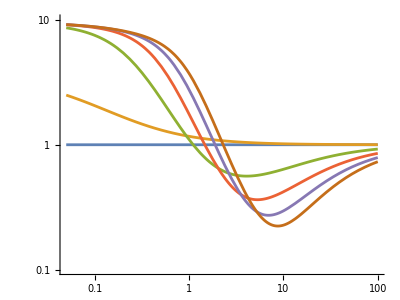

```mathematica
βE = 50;
δE = 10;
γE = 0.05;
ωE=10;
ρE = 0.0;
Show[LogLogPlot[{1,ex1[δE,βE,γE,ω,ρE],ex2[δE,βE,γE,ω,ρE],ex3[δE,βE,γE,ω,ρE],ex4[δE,βE,γE,ω,ρE,10000],ex5[δE,βE,γE,ω,ρE,10000]},{ω,1/20,100},PlotRange->{0.1,10}],TextStyle->FontSize->20,AspectRatio->0.75]
```

### δ-β plot

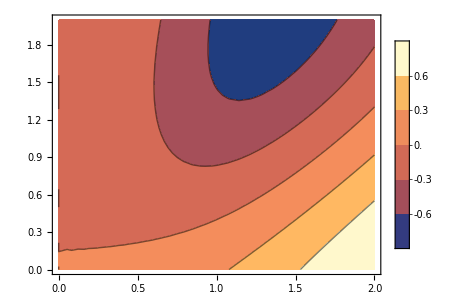

```mathematica
δE = 10;
βE = 50;
γE = 0.05;
ωE=10;
ρE = 0.0;
Show[ContourPlot[Log10[ex5[10^δ,10^β,γE,ωE,ρE,10000]],{δ,0,2},{β,0,2},PlotLegends->True,AspectRatio->0.75,PlotRange->All,Contours->5],TextStyle->FontSize->20]
```

## 5 step model with dynamics

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14]
e1 =ksyn -k1*L1*r[t]+kd1*b1[t]+kd1*p1[t]+kd1*q1[t]+kd1*f1[t]+kd1*g1[t]+kd1*h1[t]-ki*r[t]==r'[t];(*R*)
e2 = k1*L1*r[t]-kd1*b1[t]-kp*b1[t]+kdp*p1[t]-ki*b1[t]==b1'[t];(*B1*)
e3 = kp*b1[t]-kdp*p1[t]-kd1*p1[t]-kp*p1[t]+kdp*q1[t]-ki*p1[t]==p1'[t];(*P1*)
e4 = kp*p1[t]-kdp*q1[t]-kd1*q1[t]-kp*q1[t]+kdp*f1[t]-ki*q1[t]==q1'[t];
e5 = kp*q1[t]-kdp*f1[t]-kd1*f1[t]-kp*f1[t]+kdp*g1[t] - ki*f1[t]==f1'[t];
e6 = kp*f1[t]-kdp*g1[t]-kd1*g1[t]-ki*g1[t]-kp*g1[t]+kdp*h1[t]==g1'[t];
e7 = kp*g1[t]-kdp*h1[t]-kd1*h1[t]-kis*h1[t]==h1'[t];
(**)
e8 =ksyn -k2*L2*r[t]+kd2*b2[t]+kd2*p2[t]+kd2*q2[t]+kd2*f2[t]+kd2*g2[t]+kd2*h2[t]-ki*r[t]==r'[t];(*R*)
e9 = k2*L2*r[t]-kd2*b2[t]-kp*b2[t]+kdp*p2[t]-ki*b2[t]==b2'[t];(*B1*)
e10 = kp*b2[t]-kdp*p2[t]-kd2*p2[t]-kp*p2[t]+kdp*q2[t]-ki*p2[t]==p2'[t];(*P1*)
e11 = kp*p2[t]-kdp*q2[t]-kd2*q2[t]-kp*q2[t]+kdp*f2[t]-ki*q2[t]==q2'[t];
e12 = kp*q2[t]-kdp*f2[t]-kd2*f2[t]-kp*f2[t]+kdp*g2[t] - ki*f2[t]==f2'[t];
e13 = kp*f2[t]-kdp*g2[t]-kd2*g2[t]-ki*g2[t]-kp*g2[t]+kdp*h2[t]==g2'[t];
e14 = kp*g2[t]-kdp*h2[t]-kd2*h2[t]-kis*h2[t]==h2'[t];
```

### Solutions

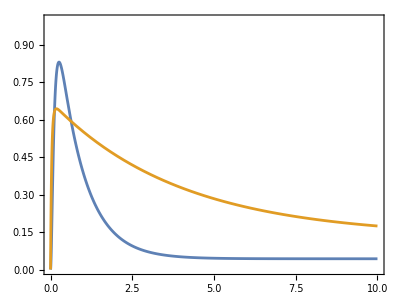

```mathematica
βE = 40;
γE = 0.05;
ωE = 20;
δE = 10;
ρE = 0.07;
eqs = {e1,e2,e3,e4,e5,e6,e7,r[0]==1,b1[0]==0,p1[0]==0,q1[0]==0,f1[0]==0,g1[0]==0,h1[0]==0}/.{kd1->1,u1->10,γ->γE,β->βE,ρ->ρE,ω->ωE};
solx=NDSolve[eqs,{r[t],b1[t],p1[t],q1[t],f1[t],g1[t],h1[t]},{t,0,1000}][[1]];
resp1[t_]=(p1[t]+q1[t]+f1[t]+g1[t]+h1[t])/.solx;
(**)
eqs = {e8,e9,e10,e11,e12,e13,e14,r[0]==1,b2[0]==0,p2[0]==0,q2[0]==0,f2[0]==0,g2[0]==0,h2[0]==0}/.{kd1->1,δ->δE,u2->2000,γ->γE,β->βE,ρ->ρE,ω->ωE};
solx=NDSolve[eqs,{r[t],b2[t],p2[t],q2[t],f2[t],g2[t],h2[t]},{t,0,1000}][[1]];
resp2[t_]=(p2[t]+q2[t]+f2[t]+g2[t]+h2[t])/.solx;
Show[Plot[{resp1[t],resp2[t]},{t,0,10}],AspectRatio->0.75,TextStyle->FontSize->20,PlotRange->{0,1},Axes->False,Frame->True]
```